```mathematica
(*First we are solving the system of ODE's, where x[t]= # of susceptible people at time t, y[t] = # infected, r[t]= # removed. Let x+y+r=1 with initial conditions below.*)
s=NDSolve[{x'[t]==-2*x[t]*y[t],y'[t]==2*x[t]*y[t]-0.5*y[t],r'[t]==0.5*y[t],x[0]==.9,y[0]==.1,r[0]==0},{x,y,r},{t,0,20}]
```

{{x→InterpolatingFunction[{{0., 20.}}, <>],y→InterpolatingFunction[{{0., 20.}}, <>],r→InterpolatingFunction[{{0., 20.}}, <>]}}

```mathematica
(*The plot shows how things will pan out given the intitial conditions where 90% of the population is susceptible to the disease and the other 10% are already infected. 
The rate of spread reaches a maximum around *)
```

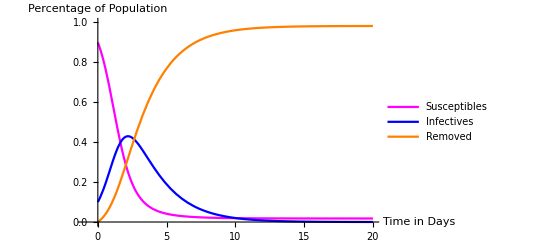

```mathematica
Plot[Evaluate[{x[t],y[t],r[t]}/.s],{t,0,20},PlotRange-> {{-1,20},{0,1}},PlotStyle->{Magenta,Blue,Orange}, PlotLegends->{"Susceptibles","Infectives","Removed"},AxesLabel->{"Time in Days","Percentage of Population"}]
```

```mathematica
(*Second Derivative Plot*)
```

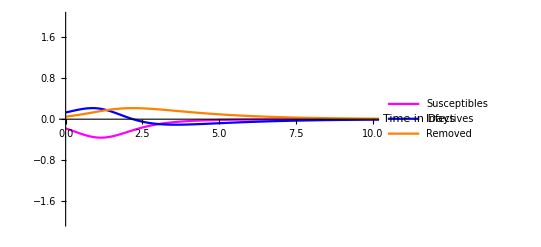

```mathematica
Plot[Evaluate[{x'[t],y'[t],r'[t]}/.s],{t,0,20},PlotRange-> {{0,10},{-2,2}},PlotStyle->{Magenta,Blue,Orange}, PlotLegends->{"Susceptibles","Infectives","Removed"},AxesLabel->{"Time in Days"}]
```

```mathematica
(*We can tell from the plot that *)
```